## Governing ODE and BCs

The above ODE describes static equilibrium for a landslide with frictional boundary conditions

-(0.284911 H[x] Sin[π x])/(1+0.18138 Cos[π x])-H'[x]==0.57735-1/(√3 (1+0.18138 Cos[π x]))+0.314159 Cos[π x]

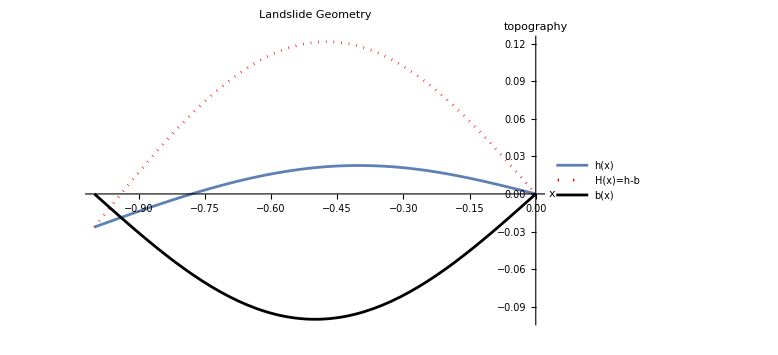

```mathematica
θv = π/6;
fv =1.0*Tan[θv]*(-x*0.0+1);
bmax = 0.1;
bv = bmax*Sin[π x];
(*bv =4 bmax*(x^2+x);(* quadratic basal topography*)*)
eqnODE = -D[H[x],x] + 0.5*Tan[θv]*D[bv,x,x]/(1+D[bv,x]*Tan[θv])*H[x] == fv+D[bv,x] -Tan[θv]/(1+D[bv,x]*Tan[θv])
solss = NDSolve[{eqnODE,H[-0]==0.0},H,{x,-1,0}];
h = bv+ H[x]/. solss;
p1=Plot[{h,H[x]/. solss,bv},{x,-1,0},PlotStyle->{DarkBlue,{Red,Dotted},Black},PlotLabel->"Landslide Geometry",AxesLabel->{"x","topography"},PlotLegends->{"h(x)","H(x)=h-b","b(x)"},ImageSize->Large,PlotRange->Full]
```

```mathematica
(*eqnODE = -D[H[x],x] + α/2*D[bv,x,x]/(1+D[bv,x]*α)*H[x] == +D[bv,x] -α/(1+D[bv,x]*α)
sol = DSolve[{eqnODE,H[1]==0},H,{x,-1,1}]//FullSimplify;
H[x]/.sol*)
```